```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
δ=0.05;
T=30;C0=1;C1=0.6;C2=0.4;C3=0.2;τ2=0.4;τ1=τ2-δ;τ3=1-δ;
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;maxtime=500;ω1=0.5;ω2=3;
t1=20;t2=21;t3=42;t4=43;t5=90;t6=91;t7=130;
t8=131;t9=150;t10=180;t11=t10+8*2Pi/ω1;t12=300;
t13=t12+30*2Pi/ω2;
t14=380;t15=390;t16=410;t17=430;t18=450;
t19=460;t20=470;t21=480;t22=490;t23=500;
Ct[t_]=Which[
t<t1,C0,
t<t2,C0+(t-t1)/(t2-t1)(C1-C0), 
t<t3,C1,
t<t4,C1+(t-t3)/(t4-t3)(C0-C1),
t<t5,C0,
t<t6,C0+(t-t5)/(t6-t5)(C2-C0), 
t<t7,C2,
t<t8,C2+(t-t7)/(t8-t7)(C0-C2),
t<t9,C0,
t<t10,C0+(t-t9)/(t10-t9) (C1-C0),
t<t11,C1 + 0.3Sin[ω1(t-t10)],
t<t12,C1,
t<t13,C1 + 0.3Sin[ω2(t-t12)],
t<t14,C1+(t-t13)/(t14-t13)(C0-C1),
t<t15,C0,
t<t16,C0+(t-t15)/(t16-t15)(C3-C0), 
t<t17,C3,
t<t18,C3+(t-t17)/(t18-t17)(C0-C3),
t<t19,C0,
t<t20,0.9,
t<t21,0.8,
t<t22,0.6,
t<t23,0.4,
True,1
];
(*Ctd[t_]=Which[
t<t1,0,
t<t2,1/(t2-t1)(C1-C0), 
t<t3,0,
t<t4,1/(t4-t3)(C0-C1),
t<t5,0,
t<t6,1/(t6-t5)(C1-C0), 
t<t7,0,
t<t8,1/(t8-t7)(C0-C1),
t<t9,0,
t<t10,1/(t10-t9) (C1-C0),
t<t11,ω1* 0.3Cos[3(t-t10)],
t<t12,0,
t<t13,ω2*0.3Cos[10(t-t12)],
t<t14,1/(t14-t13)(C0-C1),
t<t15,0,
t<t16,0,
t<t17,0,
t<t18,0,
True,1
];*)
```

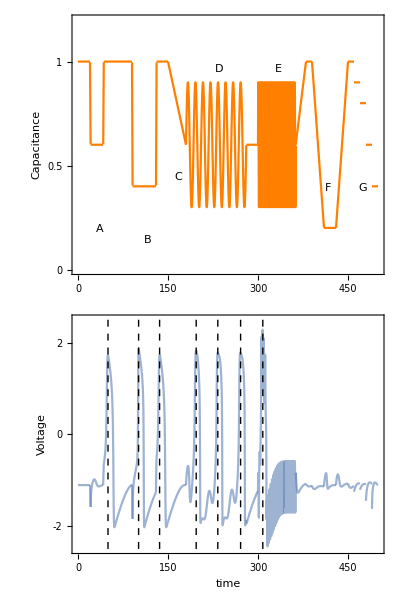

Fig0_intro.png

```mathematica
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;

(*{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.01];*)
{U1,W1}=NDSolveValue[{u'[t] ==u[t]/Ct[t]-u[t]^3/(3Ct[t]^3)-w[t],w'[t]==ep(u[t]/Ct[t]-γ w[t] + β),u[0]==Ct[0]v0,w[0]==w0},{u,w},{t,0,maxtime},MaxStepSize->0.008];
(*Voltage/capacitance plot*)
capacitance=Plot[{Ct[t]},{t,0,maxtime},PlotPoints->10000,MaxRecursion->3,PlotStyle->Orange, AspectRatio->1/6,PlotRange->{0,1.2},ImageSize->Large,ImagePadding->{{40,20},{4,5}},Frame->True,FrameLabel->{"","Capacitance"},TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},FrameTicks->{Automatic,{0,0.5,1}}];
tags=ListPlot[{
Labeled[{23,0.15},"A"]
,Labeled[{103,0.1},"B"]
,Labeled[{152,0.4},"C"]
,Labeled[{220,0.92},"D"]
,Labeled[{320,0.92},"E"]
,Labeled[{430,0.35},"F"]
,Labeled[{460,0.35},"G"]
},PlotStyle->{Opacity[0]}];
peaks = FindPeaks[Table[U1[t]/Ct[t],{t,1,maxtime,1}],2,0,1];
raster =Table[ Graphics[{Dashed, Line[{{xk[[1]],-2.5},{xk[[1]],2.5}}]}],{xk,peaks}];
voltage=Plot[U1[t]/Ct[t],{t,0,maxtime},PlotRange->{-2.5,2.5},PlotPoints->10000, AspectRatio->1/6,ImageSize->Large,ImagePadding->{{40,20},{40,3}},Frame->True,FrameLabel->{"time","Voltage"},PlotStyle->{Opacity[0.6]},FrameTicks->{Automatic,{-2,0,2}}];
(*,PlotLegends->Placed[StringJoin["ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above]*)


g1=Grid[{ {Show[capacitance,tags]},{Show[voltage,raster]}}]
(*g1=Legended[Show[, AspectRatio->1/4],LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{"Voltage","Capacitance"}]]*)
Export["Fig0_intro.png",g1]
```

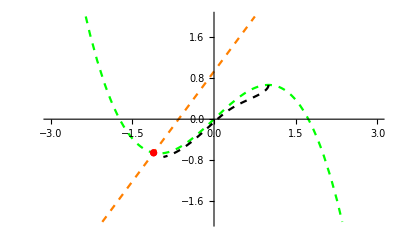

```mathematica
(*Phase plane*)
g1=ParametricPlot[{{V[t],W[t]}},{t,0,30},ColorFunction->Function[{x,y,t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False];
g2=Plot[{v-v^3/3,(v+β)/γ},{v,-3,3},PlotRange->{-2,2},PlotStyle->{{Green,Dashed},{Orange,Dashed}}];
g3=ListPlot[{{v0,w0}},PlotStyle->{Red}];
maxtimesep=26.5;
{Vsep,Wsep}=NDSolveValue[{-v'[t]== v[t]-v[t]^3/3-w[t],-w'[t]==ep(v[t]-γ w[t]+β),v[0]==1,w[0]==2/3},{v,w},{t,0,maxtimesep}];
separatrix=ParametricPlot[{Vsep[t],Wsep[t]},{t,0,maxtimesep},PlotStyle->{Black,Dashed}];
Show[g2,g1,g3,separatrix]
```